```mathematica
1.c
x={1.00,2.00,3.00,4.00,5.00};dx=0.02;y={2.8,4.7,7.1,9.4,10.8};dy=0.2;
a1=1.95; a0=1.15;
da0=0.3; da1=0.1;
sigma[i_]:= Sqrt[dy^2+ da0^2+(a1*dx)^2+(x[[i]]*da1)^2];
Sum[(y[[i]]-(a0+a1*x[[i]]))^2/sigma[[i]]^2,{i,1,5}]//N
```

2.11613

#### 1.d.ii

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.75 | 0.322128 | 2.32826 | 0.10231
X | 2.07 | 0.0971253 | 21.3127 | 0.000226009

| Estimate | Standard Error | t-Statistic | P-Value
X | 2.27455 | 0.0600895 | 37.8526 | 2.90903×10^-6

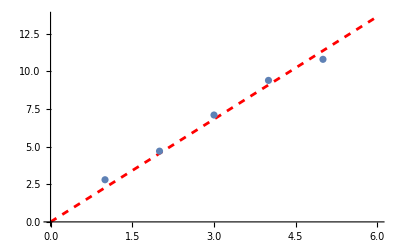

```mathematica
x={1.00,2.00,3.00,4.00,5.00};dx=0.02;y={2.8,4.7,7.1,9.4,10.8};dy=0.2;
data = Thread[{x,y}];
dataplot = ListPlot[data];
fit = LinearModelFit[data,X,X];
fit["ParameterTable"]
fit2=LinearModelFit[data, X, X, IncludeConstantBasis->False];
fit2["ParameterTable"]
fitplot = Plot[fit2[X], {X,Min[x]-1,Max[x]+1},PlotStyle->{Red, Dashed}];
Show[fitplot, dataplot]
```

### 3.

```mathematica
(*Data*)masses={50.0,100.0,150.0,200.0,250.0,300.0,350.0,400.0,450.0,500.0};
stretch={1.6,2.9,4.5,6.0,7.6,9.0,10.6,12.0,13.5,15.1};
data3=Transpose[{masses,stretch}];

(*(a) Best fit with intercept:Basis is {1,m}*)
lm3a=LinearModelFit[data3,{1,m},m];
Print["Part A Parameters: ",lm3a["ParameterTable"]];

(*(b) Best fit with zero intercept:Basis is {m} only*)
lm3b=LinearModelFit[data3,{m},m];
Print["Part B Parameters: ",lm3b["ParameterTable"]];

(*(d) Uncertainty Assessment:dx=0.2*)
chi2red=lm3a["EstimatedVariance"]/(0.2^2);
Print["Reduced Chi-Squared: ",chi2red];

(*(e) Determine k:k=g/slope.Using SI units (g->kg,cm->m)*)
slope3=lm3b["BestFitParameters"][[1]];
k3=(9.80665*0.1)/slope3; (*0.1 accounts for g/cm to kg/m conversion*)
Print["Spring Constant k: ",k3," N/m"];
```

Part A Parameters:  | Estimate | Standard Error | t-Statistic | P-Value
1 | -2.14018×10^-15 | 0.0474182 | -4.51342×10^-14 | 1
m | 0.0301091 | 0.000152843 | 196.994 | 4.93482×10^-16

Part B Parameters:  | Estimate | Standard Error | t-Statistic | P-Value
1 | -2.14018×10^-15 | 0.0474182 | -4.51342×10^-14 | 1
m | 0.0301091 | 0.000152843 | 196.994 | 4.93482×10^-16

Reduced Chi-Squared: 0.120455

Spring Constant k: -4.58216×10^14 N/m

### 4.

```mathematica
(*Data*)m4={50.0,100.0,150.0,200.0,250.0,300.0,350.0,400.0,450.0,500.0};
t4={0.26,0.34,0.43,0.49,0.55,0.60,0.65,0.70,0.74,0.78};
tSqData=Transpose[{m4,t4^2}];

(*(b) Fits:T^2=Sm+b*)
lm4a=LinearModelFit[tSqData,{1,m},m];
lm4b=LinearModelFit[tSqData,{m},m];

(*(c) Uncertainty Assessment:dT=0.05.Propagated error dy~2*T*dT*)
dyAvg=Mean[2*t4*0.05];
chi2red4=lm4a["EstimatedVariance"]/(dyAvg^2);
Print["Reduced Chi-Squared (Problem 4): ",chi2red4];

(*(d) Determine k:k=4*Pi^2/slope (in kg)*)
slope4=lm4a["BestFitParameters"][[2]];
k4=(4*Pi^2)/(slope4*1000);
Print["Oscillation k: ",k4," N/m"];
```

Reduced Chi-Squared (Problem 4): 0.00584995

Oscillation k: 32.5001 N/m

### 5.

Predicted Slope: 2.24152

Measured Slope: 22.3105

Intercept P-Value: 0.83554

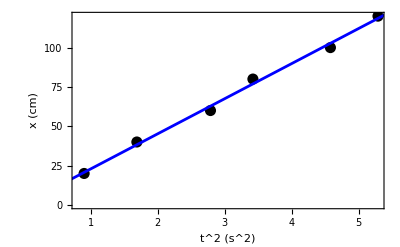

```mathematica
(*Constants*)L=12.5;h=0.08;g=9.80665;
predictedS=(5/14)*g*(h/L)*100; (*cm/s^2*)

(*Data*)
x5={20.0,40.0,60.0,80.0,100.0,120.0};
t5={0.95,1.30,1.67,1.85,2.14,2.30};
data5=Transpose[{t5^2,x5}];

(*Linear Model:x=S*t^2+b*)
lm5=LinearModelFit[data5,{1,tSq},tSq];

(*Assessment*)
Print["Predicted Slope: ",predictedS];
Print["Measured Slope: ",lm5["BestFitParameters"][[2]]];
Print["Intercept P-Value: ",lm5["ParameterPValues"][[1]]];

(*Visualize*)
Show[ListPlot[data5,PlotStyle->{PointSize[0.02],Black}],Plot[lm5[tSq],{tSq,0,6},PlotStyle->Blue],Frame->True,FrameLabel->{"t^2 (s^2)","x (cm)"}]
```